```mathematica
Basedir="/Users/yifan/Library/CloudStorage/Dropbox/Current\ Projects/2023-AlonLab-sickspans/NIA supplementary/";
RapaMetTables={
{"Lifespan_C2006_Rapa14ppm.xlsx","Rapa"},
(*{"Lifespan_C2009_Rapa42ppm.xlsx", "Rapa_mid"},*)
{"Lifespan_C2011_MetRapa.xlsx","Met"},
{"Lifespan_C2011_MetRapa.xlsx","MetRapa"}
};
RapaAc9Tables={
{"Lifespan_C2006_Rapa14ppm.xlsx","Rapa"},
(*{"Lifespan_C2009_Rapa42ppm.xlsx", "Rapa_mid"},*)
{"Lifespan_C2013_Aca8m.xlsx","ACA_mid"},
{"Lifespan_C2017_RapAc.xlsx","RaAc9"}
};
RapaAc16Tables={
{"Lifespan_C2006_Rapa14ppm.xlsx","Rapa"},
(*{"Lifespan_C2009_Rapa42ppm.xlsx", "Rapa_mid"},*)
{"Lifespan_C2012_Aca16m.xlsx","ACA"},
{"Lifespan_C2017_RapAc.xlsx","RaAc16"}
};
RapaDosageSeriesTables={
{"Lifespan_C2009_Rapa42ppm.xlsx", "Rapa_lo"},
{"Lifespan_C2009_Rapa42ppm.xlsx", "Rapa_mid"},
{"Lifespan_C2009_Rapa42ppm.xlsx", "Rapa_hi"}
};
AcaDosageSeriesTables={
{"Lifespan_C2013_Aca8m.xlsx","ACA_lo"},
{"Lifespan_C2013_Aca8m.xlsx","ACA_mid"},
{"Lifespan_C2013_Aca8m.xlsx","ACA_hi"}
};
E17aDosageSeriesTables={
{"Lifespan_C2009_Rapa42ppm.xlsx","17aE2"},
{"Lifespan_C2011_MetRapa.xlsx","17aE2_hi"}
};
NDGADosageSeriesTables={
{"Lifespan_C2010_NDGA.xlsx","NDGA_lo"},
{"Lifespan_C2010_NDGA.xlsx","NDGA_mid"},
{"Lifespan_C2010_NDGA.xlsx","NDGA_hi"},
};
AcaAgeSeriesTables={
{"Lifespan_C2009_Rapa42ppm.xlsx","ACA", 4},
{"Lifespan_C2013_Aca8m.xlsx","ACA_mid", 8},
{"Lifespan_C2012_Aca16m.xlsx","ACA", 16}
};
E17aAgeSeriesTables={
{"Lifespan_C2011_MetRapa.xlsx","17aE2_hi",10},
{"Lifespan_C2016_17aE2_16m.xlsx","17aE2_16m",16},
{"Lifespan_C2016_17aE2_16m.xlsx","17aE2_20m",20}
};
NDGAAgeSeriesTables={
{"Lifespan_C2010_NDGA.xlsx","NDGA_mid",6},
{"Lifespan_C2004_NDGA.xlsx","NDGA",9}
};
RapaAgeSeriesTables={
{"Lifespan_C2006_Rapa14ppm.xlsx","Rapa",9},
{"Lifespan_C2005_Rapa20m.xlsx","Rapa",20}
};
RapaRegimeSeriesTables={
{"Lifespan_C2015_Rapa_hi_regimes.xlsx","Rapa_hi_continuous"},
{"Lifespan_C2015_Rapa_hi_regimes.xlsx","Rapa_hi_cycle"},
{"Lifespan_C2015_Rapa_hi_regimes.xlsx","Rapa_hi_start_stop"}
};
getSetFromFilename[fn_]:=
StringTake[fn,{#[[1]]+1,#[[2]]-1}]&@(First@StringPosition[fn,RegularExpression["\\_C\\d\\d\\d\\d_"]]);
```

```mathematica
getDataFromQuery[fn_, query_]:=
(Table[
Table[
Cases[(Import@fn)[[1,2;;]],{__,g,_,q,__,_,y_,x_}:>{x,1-Round@y}]
,{q,{"Control", query}}
],{g,{"m","f"}}
]);
getTablesFromQuery[fn_, query_]:=
(Table[
Table[
Cases[(Import@fn)[[1,2;;]],{__,g,_,q,__,_,y_,x_}]
,{q,{"Control", query}}
],{g,{"m","f"}}
]);
dataLabels={{"Control ♂","Treated ♂"},{"Control ♀","Treated ♀"}};
combinationTreats=Association[#->ToExpression[#<>"Tables"]&/@{"RapaMet","RapaAc9","RapaAc16"}];
```

```mathematica
WeibullcondMLE[times_,censors_]:=(
(*conditional MLE proposed by ref [1]. Formula taken from ref [2].
1. Yang,Z.& Xie,M.Efficient estimation of the weibull shape parameter based on a modified profile likelihood.Journal of Statistical Computation and Simulation 73,115–123 (2003).
2. Makalic,E.& Schmidt,D.F.Maximum likelihood estimation of the Weibull distribution with reduced bias.Stat Comput 33,69 (2023).
*)
shortN=Min[500, Length@times];
d=Count[1.*censors,0.];
deaths=1.-censors;
(*initk=Module[{β},NMinimize[{1,Gamma[1+2/β]/Gamma[1+1/β]^2-1==N@Variance[times[[;;shortN]]]/Mean[times[[;;shortN]]]^2,β>0},β][[2,1,2]]];*)
initk=5;
k=FindRoot[(d-1)/β==d Total[times^β Log@times]/Total[times^β ]-Total[deaths*Log@times],{β,initk},AccuracyGoal->4][[1,2]];
lambda=(Total[times^k]/d)^(1/k);
{k,lambda}
);
leftTruncatedWeibullDistribution[a_,b_,L_]:=ProbabilityDistribution[a/b(x/b)^(a-1)Exp[(L/b)^a-(x/b)^a], {x, L, Infinity}];
WeibullQuantiles[k_, lambda_,qs_]:=lambda*Power[-Log@qs,1/k];
WeibullMean[k_, lambda_]:=lambda*Gamma[1+1/k];
WeibullSD[k_, lambda_]:=lambda*Sqrt[Gamma[1+2/k]-Gamma[1+1/k]^2];
WeibullGoFTest[data_,WBpars_]:=AndersonDarlingTest[Join[
RandomVariate[leftTruncatedWeibullDistribution@@Append[WBpars,#]]&/@Select[data,#[[2]]==1.&][[;;,1]],
Select[data,#[[2]]==0.&][[;;,1]]
],WeibullDistribution@@WBpars
]
```

```mathematica
survivalCurveWeibullFit[fn_,query_,bootstrapN_:100]:=
(Table[
Table[
Module[{data=Cases[(Import@fn)[[1,2;;]],{__,g,_,q,__,_,y_,x_}:>{x,1-Round@y}]},
((*Print[ToString@{fn,g,q}];*)
{WeibullGoFTest[data, Mean@#],VectorAround[{#[[1]],#[[2]]/365.}&@Mean@#,Covariance[{#[[1]],#[[2]]/365.}&/@#]]&@#}&@(WeibullcondMLE@@(#ᵀ)&/@RandomChoice[data,{bootstrapN,Length@data}])
)],{q,{"Control", query}}
],{g,{"m","f"}}
]);
WeibullFitsDict=Association[
Table[(
fn=Basedir<>entry[[1]];
(*Print[entry];*)
entry->
survivalCurveWeibullFit[fn,entry[[2]]]
),{entry,Union[Flatten[Values@combinationTreats,1]]}]
];
```

```mathematica
survivalCurveWeibullStats[fn_,query_,bootstrapN_:100]:=
(Table[
Table[
Module[{data=Cases[(Import@fn)[[1,2;;]],{__,g,_,q,__,_,y_,x_}:>{x,1-Round@y}]},
((*Print[ToString@{fn,g,q}];*)
(WeibullMean[#[[1]],#[[2]]]/{365,WeibullSD[#[[1]],#[[2]]]}&@(WeibullcondMLE@@(#ᵀ))&/@RandomChoice[data,{bootstrapN,Length@data}])
)],{q,{"Control", query}}
],{g,{"m","f"}}
]);
WeibullStatsDict=Association[
Table[(
fn=Basedir<>entry[[1]];
(*Print[entry];*)
(*entry->survivalCurveBSStats[fn,entry[[2]]]*)
entry->Map[VectorAround[Mean@#,Covariance@#]&,survivalCurveWeibullStats[fn,entry[[2]],100],{2}]
),{entry,Union[Flatten[Values@combinationTreats,1]]}]
];
```

```mathematica
survivalCurveBSStats[fn_,query_,bootstrapN_:100]:=
(Table[
Table[
Module[{data=Cases[(Import@fn)[[1,2;;]],{__,g,_,q,__,_,y_,x_}:>{x,1-Round@y}]},
(
(*Print[ToString@{fn,g,q}];*)
(TrimmedMean[#,{.1,0.}]/{365,Sqrt@TrimmedVariance[#,{.1,0.}]}&@SurvivalDistribution[EventData@@(#ᵀ),Method->"KaplanMeier"])&/@RandomChoice[data,{bootstrapN,Length@data}]
)],{q,{"Control", query}}
],{g,{"m","f"}}
]);
statsDict=Association[
Table[(
fn=Basedir<>entry[[1]];
Print[entry];
(*entry->survivalCurveBSStats[fn,entry[[2]]]*)
entry->Map[VectorAround[Mean@#,Covariance@#]&,survivalCurveBSStats[fn,entry[[2]],500],{2}]
),{entry,Union[Flatten[Values@combinationTreats,1]]}]
];
```

{Lifespan_C2006_Rapa14ppm.xlsx,Rapa}

{Lifespan_C2011_MetRapa.xlsx,Met}

{Lifespan_C2011_MetRapa.xlsx,MetRapa}

{Lifespan_C2012_Aca16m.xlsx,ACA}

{Lifespan_C2013_Aca8m.xlsx,ACA_mid}

{Lifespan_C2017_RapAc.xlsx,RaAc16}

{Lifespan_C2017_RapAc.xlsx,RaAc9}

```mathematica
generateSteps[times_,survs_]:=
Flatten[Table[{Transpose[{times,Prepend[survs[[;;-2]],1.]}][[i]],Transpose[{times,survs}][[i]]},{i,Length@times}],1]
PlotSurvWeibullFit[data_,wbpar_]:=ListLinePlot[
{generateSteps[Sort@DeleteDuplicates@data[[;;,1]] ,SurvivalFunction[SurvivalDistribution[EventData@@(dataᵀ)],Sort@DeleteDuplicates@data[[;;,1]]]],
(*Transpose@{Sort@DeleteDuplicates@data[[;;,1]] ,SurvivalFunction[SurvivalDistribution[EventData@@(dataᵀ)],Sort@DeleteDuplicates@data[[;;,1]]]},*)
Transpose@{Sort@DeleteDuplicates@data[[;;,1]],
SurvivalFunction[WeibullDistribution@@wbpar, Sort@DeleteDuplicates@data[[;;,1]]]}
},
(*AxesLabel->{ "Age/age50","Survivorship"},*)
PlotStyle->{Automatic,Directive[Dashed,Orange,Thick]},
AxesStyle->Directive[Black,Thickness[0.006]],
TicksStyle->Directive[Black,Thickness[0.004]],
AxesOrigin->{0.5,0},
PlotRange->{{0.5,4.},{0,1.04}},
Ticks->{Range[0.5,4.,0.5],Range[0.,1.,.2]}
]
WeibullGoFPlots=Association@KeyValueMap[Module[
{query=#1[[2]],set=getSetFromFilename@#1[[1]],
wbpar=#2[[;;,;;,2,1]],
datas=
getDataFromQuery[Basedir<>#1[[1]],#1[[2]]],
pvalues=#2[[;;,;;,1]]
},
#1->Table[Table[Show[PlotSurvWeibullFit[{#[[1]]/365.,#[[2]]}&/@datas[[g,q]],wbpar[[g,q]]],PlotLabel->Map[(StringRiffle[{query,set,#}]&),dataLabels,{2}][[g,q]]<>" p="<>ToString@Round[pvalues[[g,q]],0.0001]],{q,2}],{g,2}]
]&,WeibullFitsDict];
```

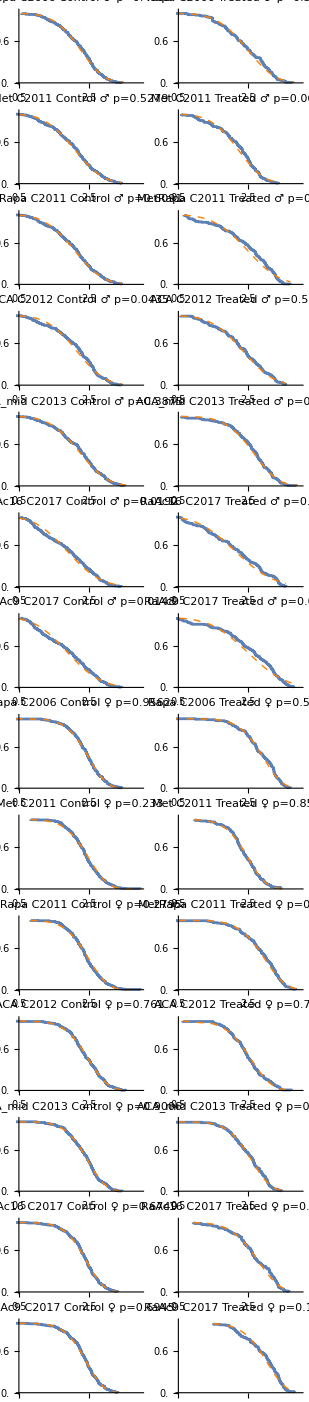

```mathematica
GraphicsGrid[Join@@Table[KeyValueMap[#2[[g,;;]]&,WeibullGoFPlots],{g,2}]]
```

{RGBColor[0.625, 0.25, 0.625],RGBColor[0.2, 1., 1.],RGBColor[0.006274509803921568, 0.40784313725490196, 0.7435294117647059],RGBColor[1, 0, 0],RGBColor[0, 1, 0],RGBColor[0.6599999999999999, 0.49, 0.32],RGBColor[0.9968627450980392, 0.4886274509803922, 0.2219607843137255],RGBColor[0.85, 0.765, 0.85]}

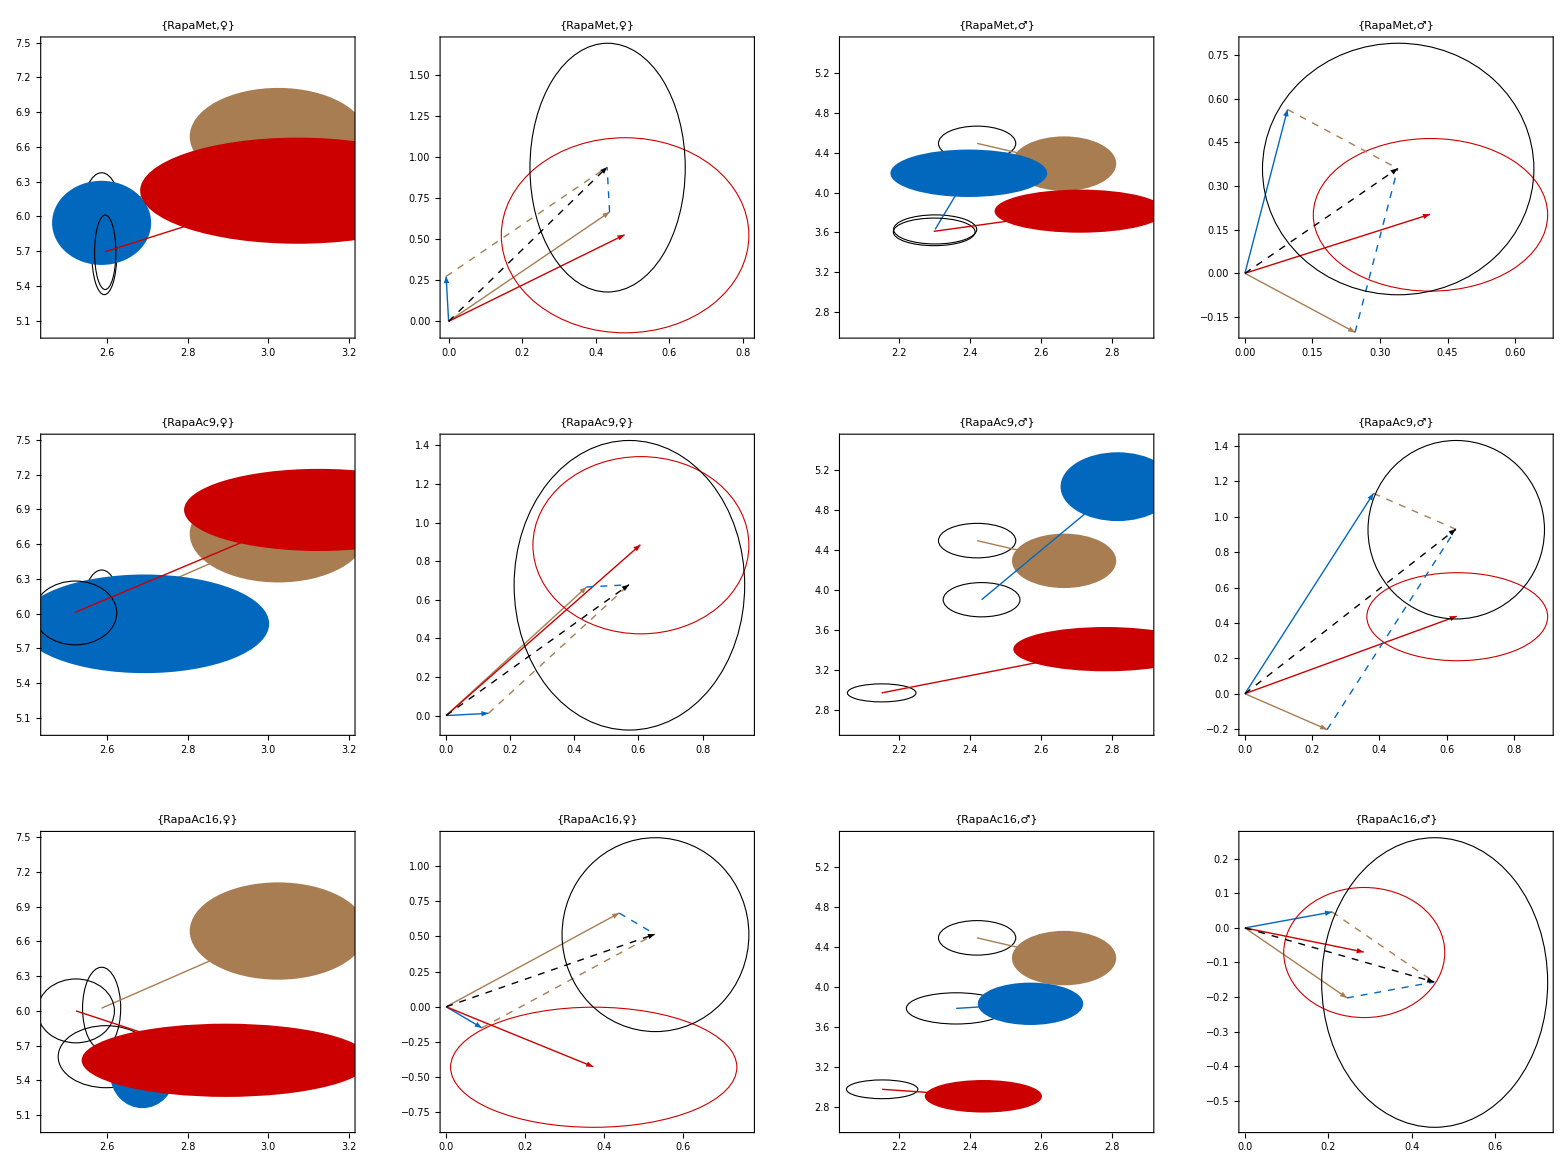

```mathematica
CombColors={Lighter[Blue,0.1],Lighter[Green,0.1],Darker[Yellow,0.2]};

pal=ColorData[3,"ColorList"][[2;;-3]];
mypal={(*Lighter[pal[[7]],0.1]*)Lighter[Purple,0.25],Lighter[Cyan,0.2],Darker[pal[[5]],0.2],Red,Green,Lighter[Brown,0.15],Lighter[pal[[1]],0.2],Darker[LightMagenta,0.15]}
CombColors={
mypal[[6]],
mypal[[3]],
(*Blend[{mypal[[6]],mypal[[3]]},.5],*)
Darker[Red,0.2]
};

combLabels=Thread[{"RapaMet","RapaAc9","RapaAc16"}->(Row/@Map[{Style["Rapa",CombColors[[1]]],Style[#[[1]],CombColors[[2]]],Style[#[[2]],CombColors[[3]]]}&,{{"Met",""},{"Ac","9"},{"Ac","16"}}])];

reverseVectorAround[v_VectorAround]:=VectorAround[Reverse@v[[1]],Reverse[Reverse@#&/@v[[2]]]];
plotRanges={{{2.05,2.9},{2.6,5.5}},{{2.45,3.2},{5.,7.5}}};
(*plotRanges={{{760,1040},{2.6,5.2}},{{900,1160},{5.2,7.1}}};*)
(*customTicks=Table[{Range@@Append[#,Round[(#[[2]]-#[[1]])/5.,0.2]],None}&/@plotRanges[[g]],{g,2}];*)
WeibullFitsCombSeriesPlots=Table[
Table[
Graphics[#,PlotLabel->Identity[{comb/.combLabels, {"♂","♀"}[[g]]}],AspectRatio->1,ImageSize->Large,Frame->True,PlotRange->plotRanges[[g]],(*FrameLabel->{"Shape","Longevity (days)"},*)FrameStyle->Directive[Black,14],Axes->False]&@Table[WeibullFitsDict[combinationTreats[comb][[i]]][[g,;;,2]]/.{x_VectorAround,y_VectorAround}:>{FaceForm[],EdgeForm[Black],Ellipsoid@@reverseVectorAround@x,FaceForm[CombColors[[i]]],
EdgeForm[],Ellipsoid@@reverseVectorAround@y,CombColors[[i]],Arrow[{Reverse@x[[1]],Reverse@y[[1]]}]},{i,3}]
,{g,{2,1}}]
,{comb,Keys@combinationTreats}];
(*GraphicsGrid@WeibullFitsCombPlots*)
WeibullFitsCombParalPlots=Table[Table[
Graphics[#,PlotLabel->Identity[{comb/.combLabels, {"♂","♀"}[[g]]}],AspectRatio->1,ImageSize->Large,Frame->True,PlotRange->All,(*FrameLabel->{"Shape","Longevity (days)"},*)FrameStyle->Directive[Black,14],Axes->False]&@Join[Table[WeibullFitsDict[combinationTreats[comb][[i]]][[g,;;,2]]/.{x_VectorAround,y_VectorAround}:>{CombColors[[i]],Arrow[{{0,0},Reverse[y[[1]]-x[[1]]]}]}
,{i,2}]
,{WeibullFitsDict[combinationTreats[comb][[3]]][[g,;;,2]]/.{x_VectorAround,y_VectorAround}:>{FaceForm[],
EdgeForm[CombColors[[3]]],Ellipsoid@@reverseVectorAround[y-x],CombColors[[3]],Arrow[{{0,0},Reverse[y[[1]]-x[[1]]]}]}
}
,{Table[WeibullFitsDict[combinationTreats[comb][[j]]][[g,;;,2]],{j,2}]/.({{x1_VectorAround,y1_VectorAround},{x2_VectorAround,y2_VectorAround}}:>{CombColors[[1]],Dashed,Line[{Reverse[y2[[1]]-x2[[1]]],Reverse[y1[[1]]-x1[[1]]+y2[[1]]-x2[[1]]]}]})
,Table[WeibullFitsDict[combinationTreats[comb][[j]]][[g,;;,2]],{j,2}]/.({{x1_VectorAround,y1_VectorAround},{x2_VectorAround,y2_VectorAround}}:>{CombColors[[2]],Dashed,Line[{Reverse[y1[[1]]-x1[[1]]],Reverse[y1[[1]]-x1[[1]]+y2[[1]]-x2[[1]]]}]})
,Table[WeibullFitsDict[combinationTreats[comb][[j]]][[g,;;,2]],{j,2}]/.({{x1_VectorAround,y1_VectorAround},{x2_VectorAround,y2_VectorAround}}:>{FaceForm[],
EdgeForm[{Dashed,Black}],Ellipsoid@@reverseVectorAround[y1-x1+y2-x2],Black,Dashed,Arrow[{{0,0},Reverse[y1[[1]]-x1[[1]]+y2[[1]]-x2[[1]]]}]})
}
]
,{g,{2,1}}]
,{comb,Keys@combinationTreats}];
(*GraphicsGrid@WeibullFitsCombParalPlots*)
GraphicsGrid@Thread[Riffle[Transpose@WeibullFitsCombSeriesPlots, Transpose@WeibullFitsCombParalPlots]]
```

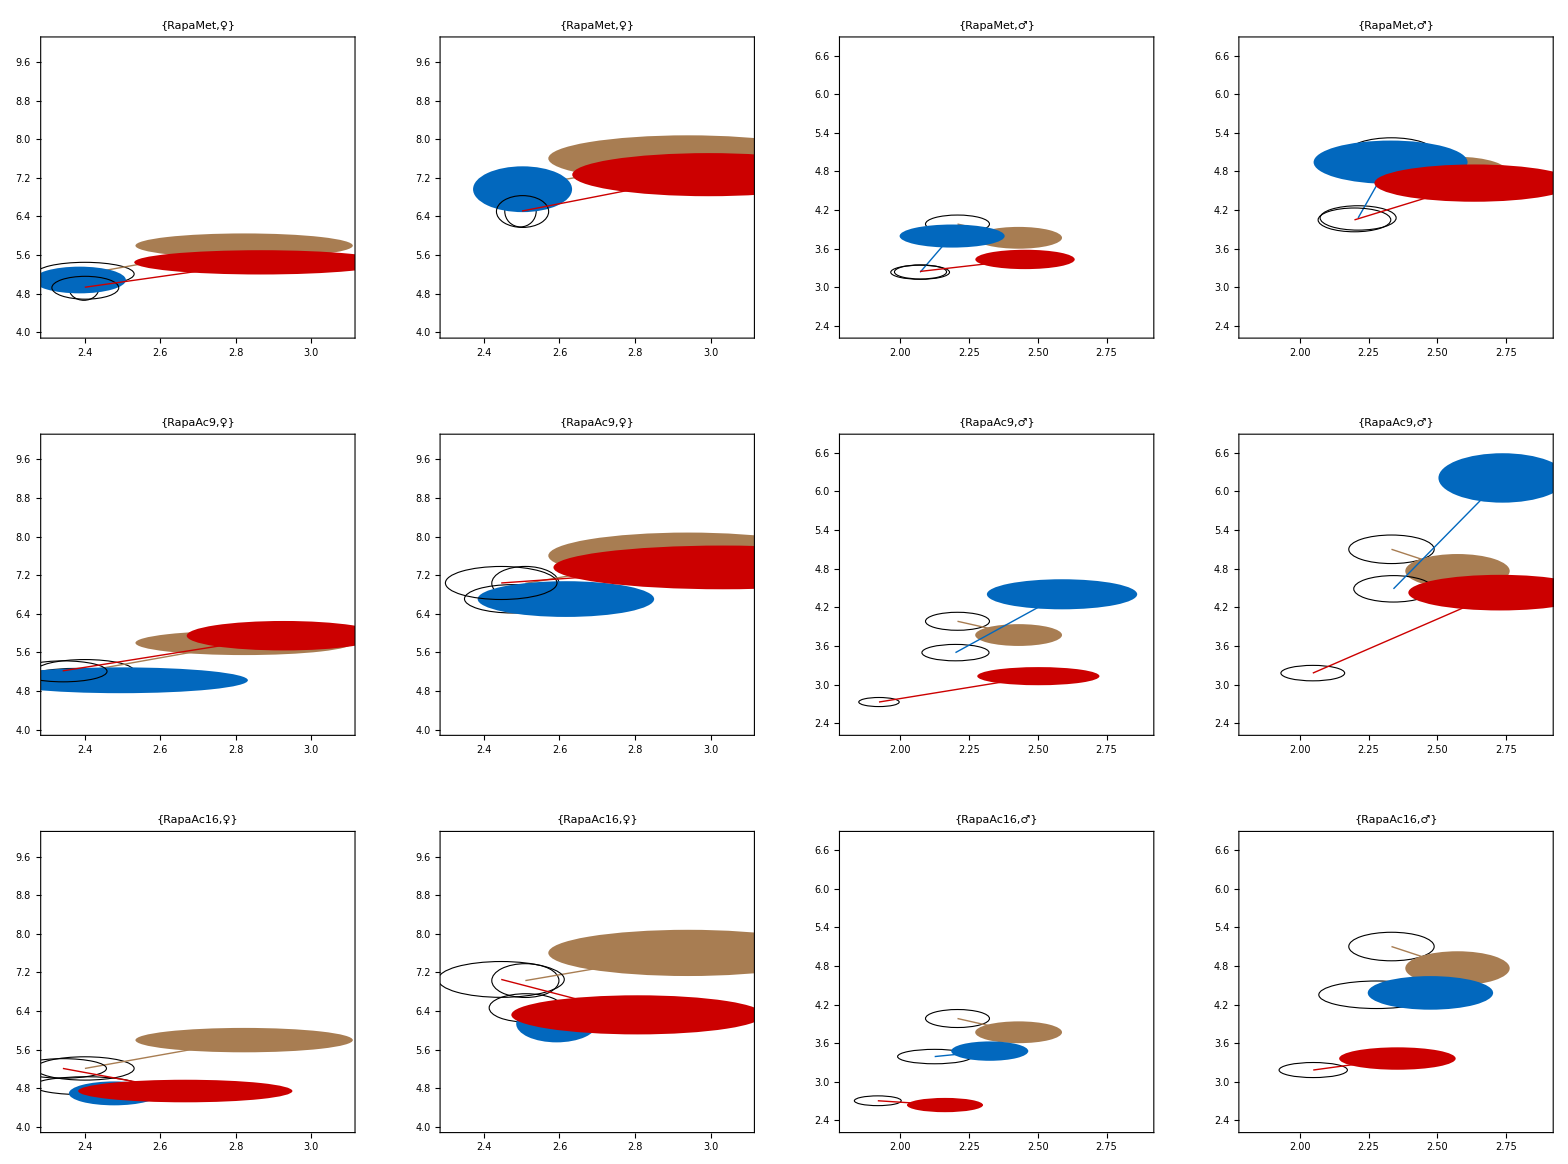

```mathematica
plotRanges={{{1.8,2.9},{2.3,6.8}},{{2.3,3.1},{4.,10.}}};
WeibullStatsCombSeriesPlots=Table[Table[
Graphics[#,PlotLabel->Identity[{comb/.combLabels, {"♂","♀"}[[g]]}],AspectRatio->1,ImageSize->Large,Frame->True,PlotRange->plotRanges[[g]],
(*FrameLabel->{"Shape","Longevity (days)"},*)FrameStyle->Directive[Black,14],Axes->False]&@Table[WeibullStatsDict[combinationTreats[comb][[i]]][[g]]/.{x_VectorAround,y_VectorAround}:>{FaceForm[],EdgeForm[Black],Ellipsoid@@x,FaceForm[CombColors[[i]]],
EdgeForm[],Ellipsoid@@y,CombColors[[i]],Arrow[{x[[1]],y[[1]]}]},{i,3}]
,{g,{2,1}}]
,{comb,Keys@combinationTreats}];
(*GraphicsGrid@WeibullStatsCombSeriesPlots*)
orderStatsCombSeriesPlots=Table[Table[
Graphics[#,PlotLabel->Identity[{comb/.combLabels, {"♂","♀"}[[g]]}],AspectRatio->1,ImageSize->Large,Frame->True,PlotRange->plotRanges[[g]],
(*FrameLabel->{"Shape","Longevity (days)"},*)FrameStyle->Directive[Black,14],Axes->False]&@Table[statsDict[combinationTreats[comb][[i]]][[g]]/.{x_VectorAround,y_VectorAround}:>{FaceForm[],EdgeForm[Black],Ellipsoid@@x,FaceForm[CombColors[[i]]],
EdgeForm[],Ellipsoid@@y,CombColors[[i]],Arrow[{x[[1]],y[[1]]}]},{i,3}]
,{g,{2,1}}]
,{comb,Keys@combinationTreats}];
(*GraphicsGrid@orderStatsCombSeriesPlots*)
GraphicsGrid@Thread[Riffle[Transpose@WeibullStatsCombSeriesPlots, Transpose@orderStatsCombSeriesPlots]]
```

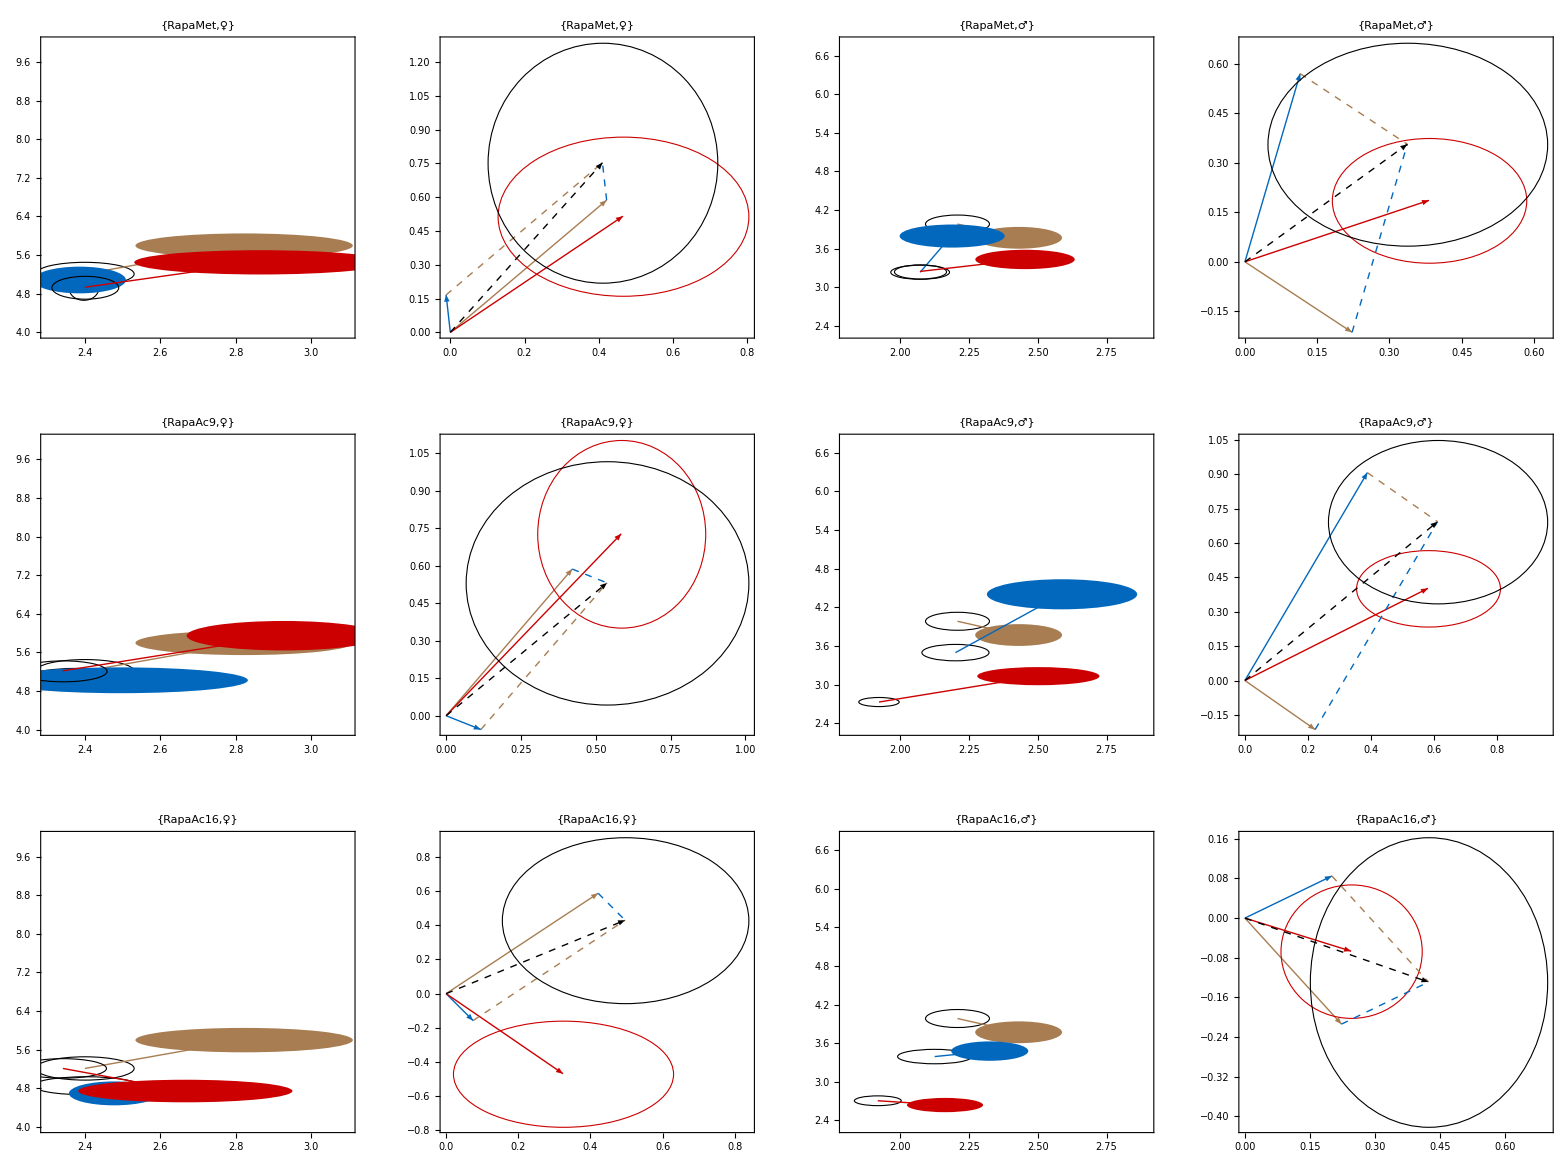
-Graphics-Longevity (years)Steepness

```mathematica
WeibullStatsCombParalPlots=Table[Table[
Graphics[#,PlotLabel->Identity[{comb/.combLabels, {"♂","♀"}[[g]]}],AspectRatio->1,ImageSize->Large,Frame->True,PlotRange->All,
(*FrameLabel->{"Shape","Longevity (days)"},*)FrameStyle->Directive[Black,14],Axes->False]&@Join[Table[WeibullStatsDict[combinationTreats[comb][[i]]][[g]]/.{x_VectorAround,y_VectorAround}:>{CombColors[[i]],Arrow[{{0,0},y[[1]]-x[[1]]}]},{i,2}]
,{WeibullStatsDict[combinationTreats[comb][[3]]][[g]]/.{x_VectorAround,y_VectorAround}:>{FaceForm[],
EdgeForm[CombColors[[3]]],Ellipsoid@@(y-x),CombColors[[3]],Arrow[{{0,0},y[[1]]-x[[1]]}]}
}
,{Table[WeibullStatsDict[combinationTreats[comb][[j]]][[g]],{j,2}]/.({{x1_VectorAround,y1_VectorAround},{x2_VectorAround,y2_VectorAround}}:>{CombColors[[1]],Dashed,Line[{y2[[1]]-x2[[1]],y1[[1]]-x1[[1]]+y2[[1]]-x2[[1]]}]})
,Table[WeibullStatsDict[combinationTreats[comb][[j]]][[g]],{j,2}]/.({{x1_VectorAround,y1_VectorAround},{x2_VectorAround,y2_VectorAround}}:>{CombColors[[2]],Dashed,Line[{y1[[1]]-x1[[1]],y1[[1]]-x1[[1]]+y2[[1]]-x2[[1]]}]})
,Table[WeibullStatsDict[combinationTreats[comb][[j]]][[g]],{j,2}]/.({{x1_VectorAround,y1_VectorAround},{x2_VectorAround,y2_VectorAround}}:>{FaceForm[],
EdgeForm[{Dashed,Black}],Ellipsoid@@(y1-x1+y2-x2),Black,Dashed,Arrow[{{0,0},y1[[1]]-x1[[1]]+y2[[1]]-x2[[1]]}]})
}
]
,{g,{2,1}}]
,{comb,Keys@combinationTreats}];
(*GraphicsGrid@orderStatsCombParalPlots*)
Panel[GraphicsGrid@Thread[Riffle[Transpose@WeibullStatsCombSeriesPlots, Transpose@WeibullStatsCombParalPlots]],{Style["Longevity (years)","Panel",16],Style[Rotate["Steepness",90Degree],"Panel",16]},{{Bottom,Center},{Left,Center}}]
```

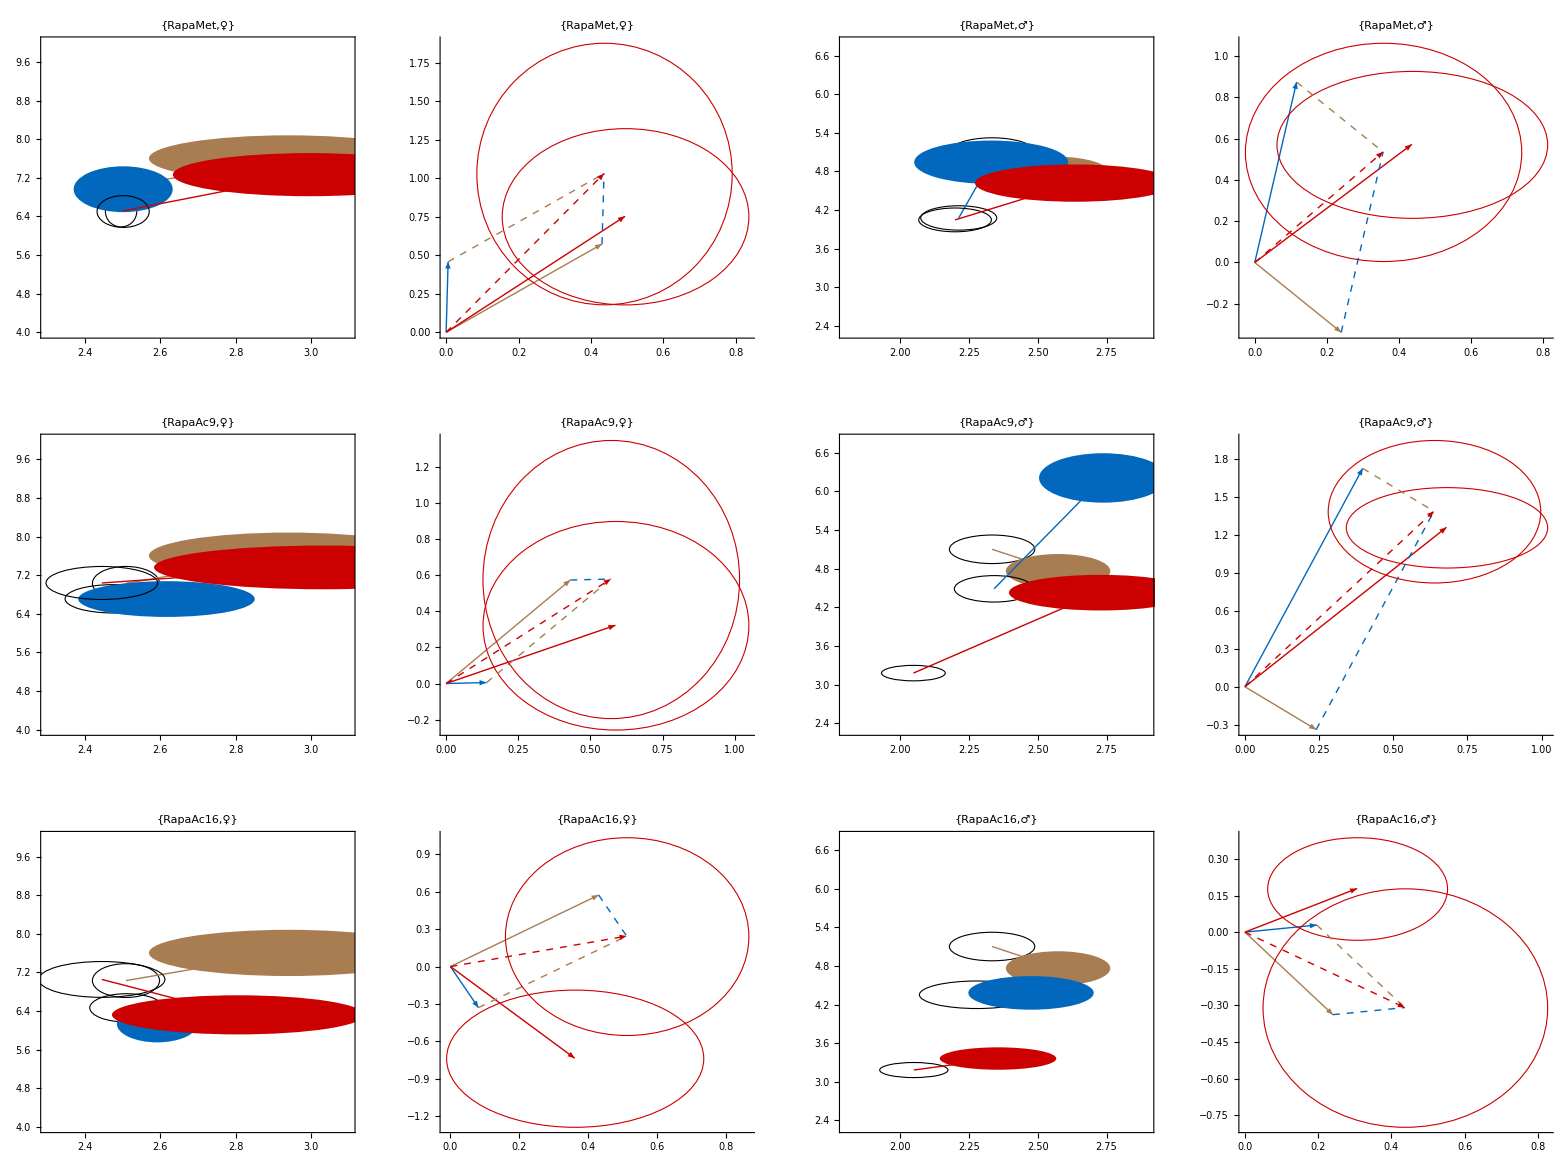
-Graphics-Longevity (years)Steepness

```mathematica
orderStatsCombParalPlots=Table[Table[
Graphics[#,PlotLabel->Identity[{comb/.combLabels, {"♂","♀"}[[g]]}],AspectRatio->1,ImageSize->Large,Frame->False,PlotRange->All,
(*FrameLabel->{"Shape","Longevity (days)"},*)AxesStyle->Directive[Black,Thickness[0.005],14],Axes->True]&@Join[Table[statsDict[combinationTreats[comb][[i]]][[g]]/.{x_VectorAround,y_VectorAround}:>{CombColors[[i]],Arrow[{{0,0},y[[1]]-x[[1]]}]},{i,2}]
,{statsDict[combinationTreats[comb][[3]]][[g]]/.{x_VectorAround,y_VectorAround}:>{FaceForm[],
EdgeForm[CombColors[[3]]],Ellipsoid@@(y-x),CombColors[[3]],Arrow[{{0,0},y[[1]]-x[[1]]}]}
}
,{Table[statsDict[combinationTreats[comb][[j]]][[g]],{j,2}]/.({{x1_VectorAround,y1_VectorAround},{x2_VectorAround,y2_VectorAround}}:>{CombColors[[1]],Dashed,Line[{y2[[1]]-x2[[1]],y1[[1]]-x1[[1]]+y2[[1]]-x2[[1]]}]})
,Table[statsDict[combinationTreats[comb][[j]]][[g]],{j,2}]/.({{x1_VectorAround,y1_VectorAround},{x2_VectorAround,y2_VectorAround}}:>{CombColors[[2]],Dashed,Line[{y1[[1]]-x1[[1]],y1[[1]]-x1[[1]]+y2[[1]]-x2[[1]]}]})
,Table[statsDict[combinationTreats[comb][[j]]][[g]],{j,2}]/.({{x1_VectorAround,y1_VectorAround},{x2_VectorAround,y2_VectorAround}}:>{FaceForm[],
EdgeForm[{Dashed,CombColors[[3]]}],Ellipsoid@@(y1-x1+y2-x2),CombColors[[3]],Dashed,Arrow[{{0,0},y1[[1]]-x1[[1]]+y2[[1]]-x2[[1]]}]})
}
]
,{g,{2,1}}]
,{comb,Keys@combinationTreats}];
(*GraphicsGrid@orderStatsCombParalPlots*)
Panel[GraphicsGrid@Thread[Riffle[Transpose@orderStatsCombSeriesPlots, Transpose@orderStatsCombParalPlots]],{Style["Longevity (years)","Panel",16],Style[Rotate["Steepness",90Degree],"Panel",16]},{{Bottom,Center},{Left,Center}}]
```

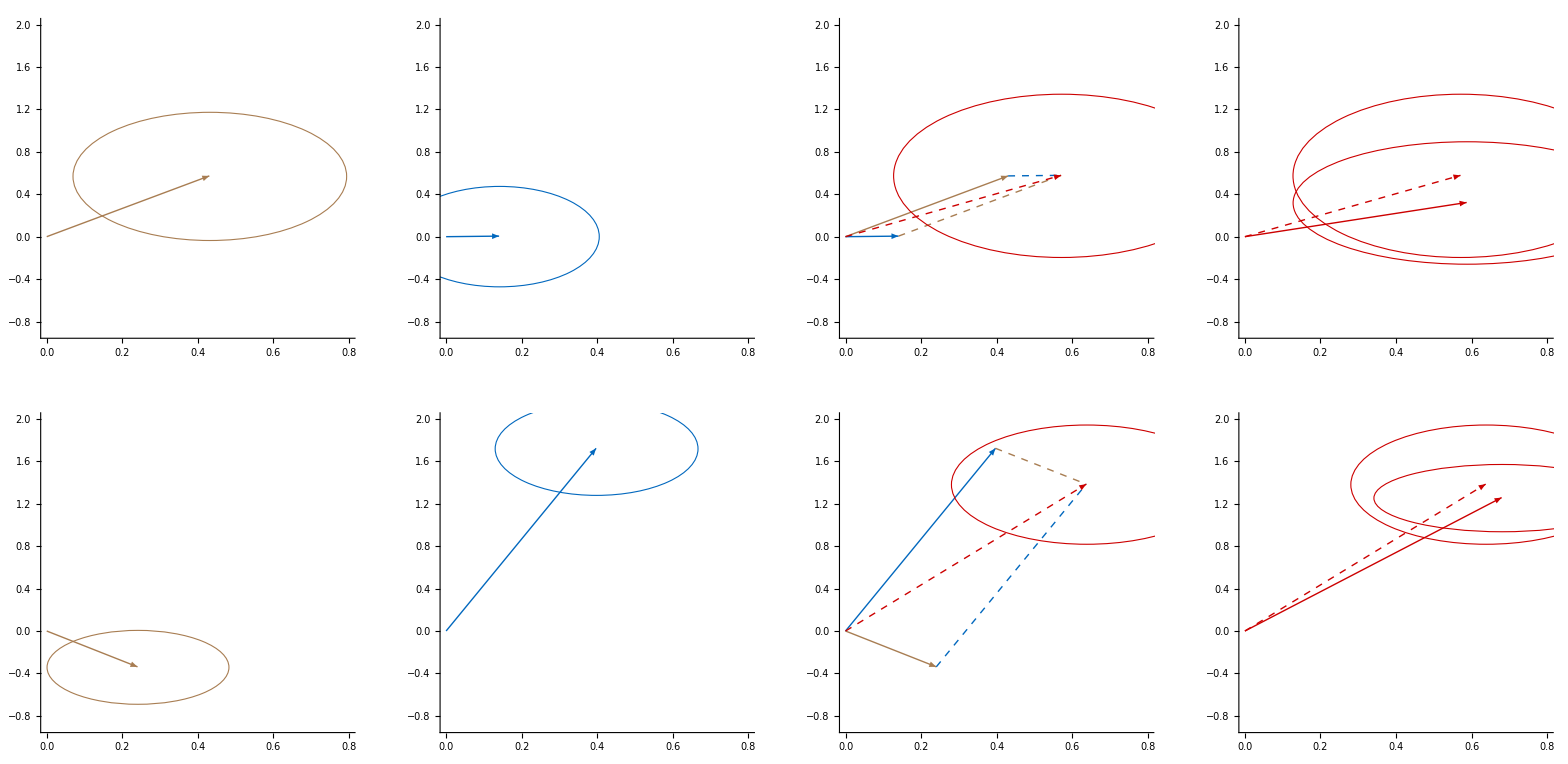

```mathematica
CombColors={
mypal[[6]],
mypal[[3]],
(*Blend[{mypal[[6]],mypal[[3]]},.5],*)
Darker[Red,0.2]
};
comb="RapaAc9";
plotRanges={
{{0.,.8},{-.9,2.}},
{{0.,.8},{-.9,2.}}
};
RaAcSepParalPlots=Table[
Graphics[#,(*PlotLabel->Identity[{comb/.combLabels, {"♂","♀"}[[g]]}],*)AspectRatio->1,ImageSize->Medium,Frame->False,PlotRange->plotRanges[[g]],
(*FrameLabel->{"Shape","Longevity (days)"},*)AxesStyle->Directive[Black,Thickness[0.005],14],Axes->True]&/@Join[
Table[statsDict[combinationTreats[comb][[i]]][[g]]/.{x_VectorAround,y_VectorAround}:>{FaceForm[],
EdgeForm[CombColors[[i]]],Ellipsoid@@(y-x),CombColors[[i]],Arrow[{{0,0},y[[1]]-x[[1]]}]},{i,2}],
{Join[
Table[statsDict[combinationTreats[comb][[i]]][[g]]/.{x_VectorAround,y_VectorAround}:>{FaceForm[],CombColors[[i]],Arrow[{{0,0},y[[1]]-x[[1]]}]},{i,2}],
Table[statsDict[combinationTreats[comb][[j]]][[g]],{j,2}]/.({{x1_VectorAround,y1_VectorAround},{x2_VectorAround,y2_VectorAround}}:>{CombColors[[1]],Dashed,Line[{y2[[1]]-x2[[1]],y1[[1]]-x1[[1]]+y2[[1]]-x2[[1]]}],
																																CombColors[[2]],Dashed,Line[{y1[[1]]-x1[[1]],y1[[1]]-x1[[1]]+y2[[1]]-x2[[1]]}]}),
Table[statsDict[combinationTreats[comb][[j]]][[g]],{j,2}]/.({{x1_VectorAround,y1_VectorAround},{x2_VectorAround,y2_VectorAround}}:>{FaceForm[],EdgeForm[{Dashed,CombColors[[3]]}],Ellipsoid@@(y1-x1+y2-x2),
																																CombColors[[3]],Dashed,Arrow[{{0,0},y1[[1]]-x1[[1]]+y2[[1]]-x2[[1]]}]})
	],
{Table[statsDict[combinationTreats[comb][[j]]][[g]],{j,2}]/.({{x1_VectorAround,y1_VectorAround},{x2_VectorAround,y2_VectorAround}}:>{FaceForm[],EdgeForm[{Dashed,CombColors[[3]]}],Ellipsoid@@(y1-x1+y2-x2),CombColors[[3]],Dashed,Arrow[{{0,0},y1[[1]]-x1[[1]]+y2[[1]]-x2[[1]]}]})
,statsDict[combinationTreats[comb][[3]]][[g]]/.{x_VectorAround,y_VectorAround}:>{FaceForm[],EdgeForm[CombColors[[3]]],Ellipsoid@@(y-x),CombColors[[3]],Arrow[{{0,0},y[[1]]-x[[1]]}]}
}
}
]
,{g,{2,1}}];
GraphicsGrid@RaAcSepParalPlots
```

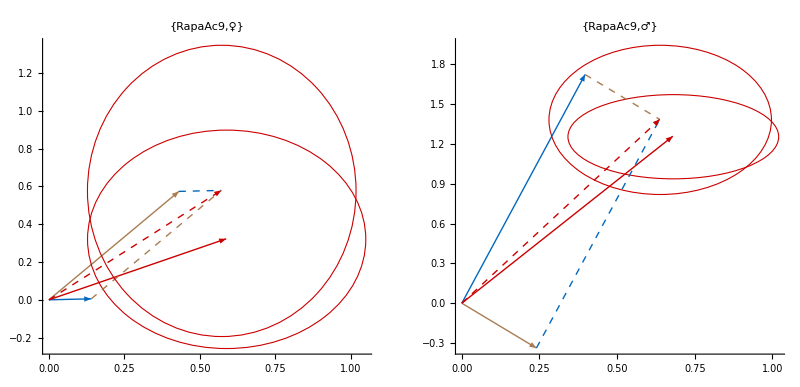
-Graphics-Longevity (years)Steepness

```mathematica
Panel[GraphicsGrid[{ orderStatsCombParalPlots[[2]]}],{Style["Longevity (years)","Panel",16],Style[Rotate["Steepness",90Degree],"Panel",16]},{{Bottom,Center},{Left,Center}}]
```

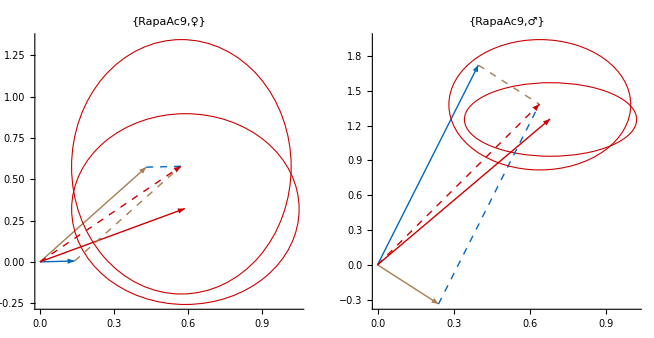

```mathematica
Legended[
GraphicsGrid[{ orderStatsCombParalPlots[[2]]}],
LineLegend[{CombColors[[1]],CombColors[[2]],{CombColors[[3]],Dashed},CombColors[[3]]},{"Rapamycin","Acarbose","Additive model","Rapamycin+Acarbose"}]
]
```

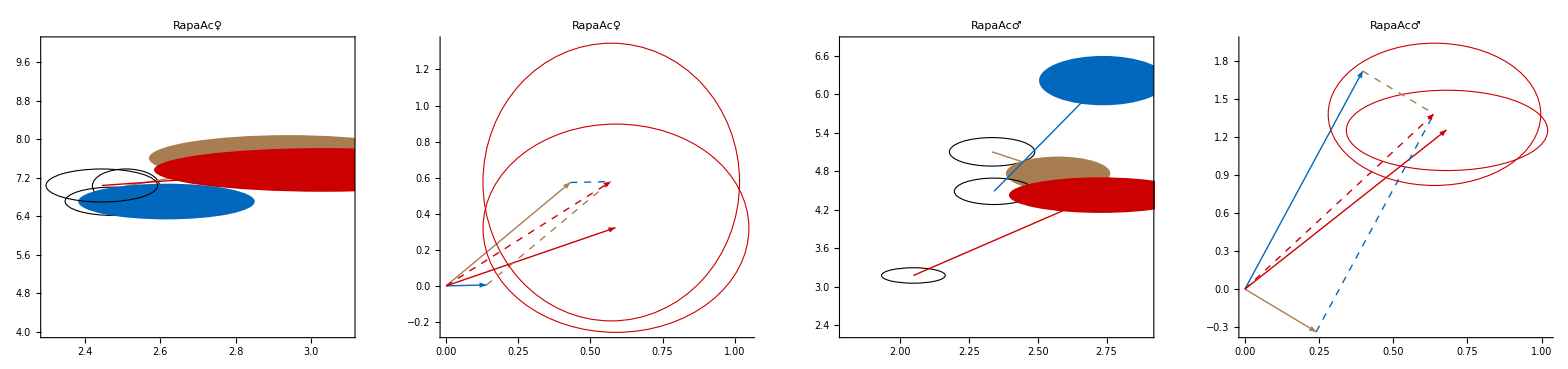
-Graphics-Longevity (years)Steepness

```mathematica
labels=Row@{Style["Rapa",Blue],Style["Ac",Green],Style[#,Black]}&/@{"♀","♂"};
Panel[GraphicsGrid[{Riffle[
Show[#[[1]],PlotLabel->#[[2]]]&/@Transpose@{orderStatsCombSeriesPlots[[2]],labels},
Show[#[[1]],PlotLabel->#[[2]]]&/@Transpose@{orderStatsCombParalPlots[[2]],labels}
]}],{Style["Longevity (years)","Panel",16],Style[Rotate["Steepness",90Degree],"Panel",16]},{{Bottom,Center},{Left,Center}}]
```

```mathematica
VectorAroundZeroTest[v_VectorAround]:=Dot[Inverse@Transpose@CholeskyDecomposition@v[[2]],v[[1]]]
```

```mathematica
Association@Table[{"m","f"}[[g]]->KeyValueMap[
#1->({(#[[3]]-#[[1]]-#[[2]]),(#[[1]]+#[[2]])}&@Cases[WeibullFitsDict[#][[g,;;,2]]&/@#2,{x_VectorAround,y_VectorAround}:>y-x])&
,combinationTreats],{g,2}]
```

<|m→{RapaMet→{VectorAround[{-0.157361,0.0717006},{{0.400615,0.0434888},{0.0434888,0.0130356}}],VectorAround[{0.359926,0.339206},{{0.269243,0.0258199},{0.0258199,0.00805821}}]},RapaAc9→{VectorAround[{-0.491539,0.00300139},{{0.443417,0.0420073},{0.0420073,0.013884}}],VectorAround[{0.92946,0.627036},{{0.315893,0.0211208},{0.0211208,0.00723909}}]},RapaAc16→{VectorAround[{0.086727,-0.16867},{{0.305493,0.0377064},{0.0377064,0.0157867}}],VectorAround[{-0.156524,0.453362},{{0.24115,0.0222403},{0.0222403,0.00752391}}]}},f→{RapaMet→{VectorAround[{-0.412365,0.0475901},{{1.07903,0.03029},{0.03029,0.00701058}}],VectorAround[{0.939965,0.431247},{{0.614789,0.0133239},{0.0133239,0.00441414}}]},RapaAc9→{VectorAround[{0.207456,0.0358819},{{1.00891,0.0415559},{0.0415559,0.0073665}}],VectorAround[{0.677681,0.570144},{{0.687679,0.0233686},{0.0233686,0.00437129}}]},RapaAc16→{VectorAround[{-0.942567,-0.156215},{{0.835755,0.0372793},{0.0372793,0.00838699}}],VectorAround[{0.516208,0.528496},{{0.526083,0.0154044},{0.0154044,0.00463184}}]}}|>

```mathematica
Association@Table[{"m","f"}[[g]]->KeyValueMap[
#1->(VectorAroundZeroTest@(#[[3]]-#[[1]]-#[[2]])&@Cases[WeibullFitsDict[#][[g,;;,2]]&/@#2,{x_VectorAround,y_VectorAround}:>y-x])&
,combinationTreats],{g,2}]
```

<|m→{RapaMet→{-0.248618,0.973655},RapaAc9→{-0.738162,0.49806},RapaAc16→{0.156911,-1.70005}},f→{RapaMet→{-0.396976,0.753824},RapaAc9→{0.206538,0.36353},RapaAc16→{-1.03103,-1.39232}}|>